Look at the Latex file for deriving the equations

```mathematica
EFL[f1_,f2_,d_]:=(f1 f2)/(f1+f2-d)(*Effective focal length*)
FP[f1_,f2_,d_]:=(f1 f2)/(f1+f2-d)(1-d/f1) (*Focal plane wrt the second lens. Positive means on the right of the lens*)
yim[f1_,f2_,d_,θ_]:=(f1 f2)/(f1+f2-d)θ (*Image height*)
```

Given f1, f2, θ, and the image height y, what is the inter-lens distance d?

```mathematica
d[f1_,f2_,θ_,y_]:=f1+f2-f1 f2 θ/y (*Inter-lens distance*)
```

Where is the focal plane wrt the second lens?

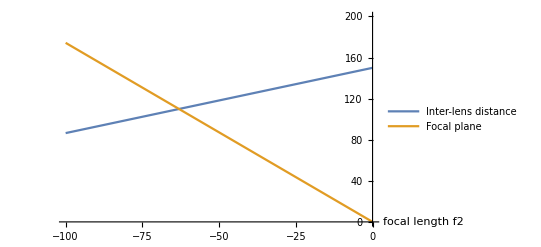

```mathematica
f1=150;
θ=1.04432*π/180;(*Incident angle. In the 'Beamsplitter parameter' nb, look at the centered angle AT THE OBJECTIVE for beam No.1 = beam No.16*)
ymax=15./2;(*Position of beam No.16 on the PMT wrt the symmetry axis. There are 16 channels with 15 interspaces of 1mm. Therefore, ymax = (16-1)/2 *)
Plot[{d[f1,f2,θ,ymax],FP[f1,f2,d[f1,f2,θ,ymax]]},{f2,-100,0},AxesLabel->{"focal length f2",""},PlotRange->{0,200},PlotLegends-> {"Inter-lens distance","Focal plane"}]
(*conclusion: longer |f2|, shorter d, longer FP*)
```

```mathematica
f2=-50;
Plot[{d[f1,f2,θ,ymax],FP[f1,f2,d[f1,f2,θ,ymax]]},{f1,0,200},AxesLabel->{"f1",""},PlotRange->{0,600},PlotLegends-> {"Inter-lens distance","Focal plane"}];
(*conclusion: longer f1, longer d, shorter FP*)
```

```mathematica
f2=-50;
d[f1,f2,θ,ymax]
FP[f1,f2,d[f1,f2,θ,ymax]]
d[f1,f2,θ,ymax]+FP[f1,f2,d[f1,f2,θ,ymax]]
```

118.227

87.1605

205.387